```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,δ,t,ϵ]],B:=Inverse[β[ω,δ,t,ϵ]],T1:=T1[t]},Do[J=Inverse[IdentityMatrix[14]-B.ConjugateTranspose[T1].J.T1].B,8000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
Clear[SR,SL]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:=Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

```mathematica
tr[1,0.0001,1,0]
```

2.99292

```mathematica
pris:=pris= Table[{ω,Abs[tr[ω,0.0001,1,0]]},{ω,Range[0,3,0.01]}]
```

```mathematica
pris
```

{{0.,2.8×10^-7},{0.01,2.8081×10^-7},{0.02,2.83264×10^-7},{0.03,2.87439×10^-7},{0.04,2.93463×10^-7},{0.05,3.01536×10^-7},{0.06,3.11935×10^-7},{0.07,3.25045×10^-7},{0.08,3.41391×10^-7},{0.09,3.61694×10^-7},{0.1,3.86954×10^-7},{0.11,4.18578×10^-7},{0.12,4.58598×10^-7},{0.13,5.10023×10^-7},{0.14,5.77474×10^-7},{0.15,6.68349×10^-7},{0.16,7.95126×10^-7},{0.17,9.803×10^-7},{0.18,1.26801×10^-6},{0.19,1.75544×10^-6},{0.2,2.69447×10^-6},{0.21,4.92698×10^-6},{0.22,0.0000129427},{0.23,0.000120119},{0.24,0.999916},{0.25,0.999991},{0.26,0.999998},{0.27,1.},{0.28,0.999998},{0.29,0.999999},{0.3,0.999999},{0.31,0.999946},{0.32,0.999915},{0.33,0.999952},{0.34,0.999996},{0.35,0.999822},{0.36,0.999769},{0.37,0.999735},{0.38,1.},{0.39,0.999893},{0.4,0.99963},{0.41,1.00011},{0.42,1.99987},{0.43,1.99945},{0.44,1.99999},{0.45,1.99952},{0.46,1.99971},{0.47,1.99943},{0.48,1.99973},{0.49,1.99925},{0.5,1.99995},{0.51,1.99998},{0.52,1.99872},{0.53,1.99903},{0.54,1.99915},{0.55,1.99899},{0.56,1.99923},{0.57,1.99871},{0.58,1.9985},{0.59,1.99935},{0.6,1.9983},{0.61,1.99973},{0.62,1.99964},{0.63,1.99728},{0.64,1.99869},{0.65,1.99639},{0.66,1.99654},{0.67,1.99915},{0.68,1.99865},{0.69,1.99668},{0.7,1.99573},{0.71,1.99501},{0.72,1.99995},{0.73,1.99796},{0.74,1.99942},{0.75,1.99859},{0.76,1.99888},{0.77,1.99973},{0.78,1.99422},{0.79,1.99392},{0.8,1.99748},{0.81,1.99466},{0.82,1.99673},{0.83,1.99427},{0.84,1.99729},{0.85,2.99415},{0.86,2.99738},{0.87,2.9969},{0.88,2.99368},{0.89,2.99688},{0.9,2.99703},{0.91,2.99826},{0.92,2.99306},{0.93,2.99479},{0.94,2.99702},{0.95,2.99795},{0.96,2.99838},{0.97,2.99731},{0.98,2.99533},{0.99,2.99384},{1.,2.99292},{1.01,2.99364},{1.02,2.99578},{1.03,2.99662},{1.04,2.99781},{1.05,2.99861},{1.06,2.99696},{1.07,2.99589},{1.08,2.99219},{1.09,2.9932},{1.1,2.99975},{1.11,2.99456},{1.12,2.99765},{1.13,2.99223},{1.14,2.99549},{1.15,2.99935},{1.16,2.99916},{1.17,2.99604},{1.18,2.99491},{1.19,2.99388},{1.2,2.99225},{1.21,2.99619},{1.22,2.99985},{1.23,2.99859},{1.24,2.99607},{1.25,2.99439},{1.26,2.99278},{1.27,2.99171},{1.28,2.99009},{1.29,2.99517},{1.3,2.99131},{1.31,2.99452},{1.32,2.99871},{1.33,2.99407},{1.34,2.99995},{1.35,2.99374},{1.36,2.99898},{1.37,2.99554},{1.38,2.99573},{1.39,2.99695},{1.4,2.991},{1.41,2.99716},{1.42,2.99663},{1.43,2.99259},{1.44,2.99574},{1.45,2.99645},{1.46,2.99659},{1.47,2.99298},{1.48,2.99688},{1.49,2.99598},{1.5,2.99759},{1.51,2.99686},{1.52,2.99775},{1.53,2.99612},{1.54,2.99757},{1.55,2.99537},{1.56,2.99078},{1.57,2.99069},{1.58,2.99396},{1.59,2.99454},{1.6,2.99467},{1.61,2.99472},{1.62,2.9927},{1.63,2.9921},{1.64,2.99471},{1.65,2.99782},{1.66,2.99345},{1.67,2.99714},{1.68,2.9918},{1.69,2.99801},{1.7,2.99855},{1.71,2.9991},{1.72,2.9991},{1.73,2.99487},{1.74,2.9974},{1.75,2.99466},{1.76,2.99766},{1.77,1.99834},{1.78,1.99608},{1.79,1.99395},{1.8,1.99764},{1.81,1.99978},{1.82,1.99923},{1.83,1.99669},{1.84,1.99756},{1.85,1.99419},{1.86,1.99449},{1.87,1.99911},{1.88,1.99467},{1.89,1.99628},{1.9,1.99475},{1.91,1.99973},{1.92,1.99872},{1.93,1.99955},{1.94,1.99567},{1.95,1.99658},{1.96,1.99597},{1.97,1.99901},{1.98,1.99937},{1.99,1.99601},{2.,1.9979},{2.01,1.99629},{2.02,1.99987},{2.03,1.99932},{2.04,1.99719},{2.05,1.99723},{2.06,1.99969},{2.07,1.99981},{2.08,1.99704},{2.09,1.9971},{2.1,1.99995},{2.11,1.99965},{2.12,1.99871},{2.13,1.99995},{2.14,1.99908},{2.15,1.99907},{2.16,1.99869},{2.17,1.99998},{2.18,1.99832},{2.19,1.99819},{2.2,1.99945},{2.21,1.9987},{2.22,1.99985},{2.23,1.99987},{2.24,1.99901},{2.25,1.99902},{2.26,1.99933},{2.27,1.99996},{2.28,1.99936},{2.29,1.99901},{2.3,1.99895},{2.31,1.99899},{2.32,1.99904},{2.33,1.99916},{2.34,1.99957},{2.35,2.},{2.36,1.9993},{2.37,1.99999},{2.38,1.99988},{2.39,1.99998},{2.4,1.99953},{2.41,1.99974},{2.42,0.999707},{2.43,1.},{2.44,0.999808},{2.45,0.999992},{2.46,0.99971},{2.47,0.999831},{2.48,0.999838},{2.49,0.999799},{2.5,0.999848},{2.51,0.999922},{2.52,0.99992},{2.53,0.999886},{2.54,0.999958},{2.55,0.999932},{2.56,0.999992},{2.57,0.999952},{2.58,0.999996},{2.59,0.999968},{2.6,0.999968},{2.61,0.999988},{2.62,0.999995},{2.63,0.999995},{2.64,0.999997},{2.65,1.},{2.66,0.999996},{2.67,1.},{2.68,0.999999},{2.69,1.},{2.7,0.999998},{2.71,1.},{2.72,1.},{2.73,0.999999},{2.74,1.},{2.75,1.},{2.76,1.},{2.77,1.},{2.78,0.999999},{2.79,0.999999},{2.8,0.999999},{2.81,0.999998},{2.82,0.999997},{2.83,0.999992},{2.84,0.999958},{2.85,0.000496198},{2.86,0.0000165305},{2.87,4.97473×10^-6},{2.88,2.35363×10^-6},{2.89,1.36412×10^-6},{2.9,8.87821×10^-7},{2.91,6.22951×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7}}

```mathematica
Clear[lista,imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14,imp,b,misfit ]
```

```mathematica
misfit[ϵ1_,y_,x_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}],tra,imp1,imp2,imp3,imp4,imp5,imp6,lista,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14,imp},
imp1[ω_]:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2[ω_]:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3[ω_]:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4[ω_]:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5[ω_]:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6[ω_]:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7[ω_]:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8[ω_]:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9[ω_]:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10[ω_]:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11[ω_]:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12[ω_]:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13[ω_]:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14[ω_]:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp[ω_]:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]];
(*lista={{imp[ω],imp[ω],imp12[ω],imp[ω],imp11[ω],imp1[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp6[ω],imp[ω],imp[ω],imp[ω],imp14[ω],imp1[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp3[ω],imp[ω],imp[ω],imp1[ω],imp2[ω],imp[ω],imp[ω],imp[ω],imp4[ω],imp[ω],imp[ω],imp11[ω],imp[ω],imp8[ω],imp[ω],imp[ω],imp[ω],imp12[ω],imp1[ω],imp[ω],imp[ω],imp1[ω],imp[ω],imp3[ω],imp[ω],imp14[ω],imp5[ω],imp[ω],imp2[ω],imp5[ω],imp[ω],imp4[ω],imp[ω],imp[ω],imp[ω],imp9[ω],imp[ω],imp[ω],imp[ω],imp14[ω],imp[ω],imp6[ω],imp1[ω],imp[ω],imp[ω],imp[ω],imp10[ω],imp7[ω],imp[ω],imp[ω],imp[ω],imp5[ω],imp1[ω],imp[ω],imp8[ω],imp10[ω],imp6[ω],imp5[ω],imp[ω],imp4[ω],imp1[ω],imp[ω],imp2[ω],imp[ω],imp7[ω],imp[ω],imp8[ω],imp13[ω],imp2[ω],imp14[ω],imp11[ω],imp9[ω],imp[ω],imp7[ω],imp5[ω]}};*)
tra[ω_,startl_,stopl_]:=Module[{},
lista={{imp[ω],imp[ω],imp12[ω],imp[ω],imp11[ω],imp1[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp6[ω],imp[ω],imp[ω],imp[ω],imp14[ω],imp1[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp3[ω],imp[ω],imp[ω],imp1[ω],imp2[ω],imp[ω],imp[ω],imp[ω],imp4[ω],imp[ω],imp[ω],imp11[ω],imp[ω],imp8[ω],imp[ω],imp[ω],imp[ω],imp12[ω],imp1[ω],imp[ω],imp[ω],imp1[ω],imp[ω],imp3[ω],imp[ω],imp14[ω],imp5[ω],imp[ω],imp2[ω],imp5[ω],imp[ω],imp4[ω],imp[ω],imp[ω],imp[ω],imp9[ω],imp[ω],imp[ω],imp[ω],imp14[ω],imp[ω],imp6[ω],imp1[ω],imp[ω],imp[ω],imp[ω],imp10[ω],imp7[ω],imp[ω],imp[ω],imp[ω],imp5[ω],imp1[ω],imp[ω],imp8[ω],imp10[ω],imp6[ω],imp5[ω],imp[ω],imp4[ω],imp1[ω],imp[ω],imp2[ω],imp[ω],imp7[ω],imp[ω],imp8[ω],imp13[ω],imp2[ω],imp14[ω],imp11[ω],imp9[ω],imp[ω],imp7[ω],imp5[ω]}};
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,startl,stopl}];J=J];Il1=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1= Il1-ConjugateTranspose[Il1];grr1= Ir1-ConjugateTranspose[Ir1];Gnonlocal1= SR[ω,0.0001,1,0].T.Il1;GNON1= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
m1=Table[{ω,tra[ω,1,20]},{ω,Range[0,3,0.01]}];
m2=Table[{ω,tra[ω,21,40]},{ω,Range[0,3,0.01]}];m3=Table[{ω,tra[ω,41,60]},{ω,Range[0,3,0.01]}];m4=Table[{ω,tra[ω,61,80]},{ω,Range[0,3,0.01]}];m5=Table[{ω,tra[ω,81,100]},{ω,Range[0,3,0.01]}];υ1=Module[{},
ρ2:=Module[{B1=Transpose[{m1[[1;;300]][[;;,1]],(m1[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/2imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m1[[1;;300]][[;;,1]],(m1[[1;;300,2]]-Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/3imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m1[[1;;300]][[;;,1]],(m1[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/4imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m1[[1;;300]][[;;,1]],(m1[[1;;300,2]]-Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/5imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m1[[1;;300]][[;;,1]],(m1[[1;;300,2]]-Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/6imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m1[[1;;300]][[;;,1]],(m1[[1;;300,2]]-Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/7imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7}];υ2=Module[{},
ρ2:=Module[{B1=Transpose[{m2[[1;;300]][[;;,1]],(m2[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/2imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m2[[1;;300]][[;;,1]],(m2[[1;;300,2]]-Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/3imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m2[[1;;300]][[;;,1]],(m2[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/4imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m2[[1;;300]][[;;,1]],(m2[[1;;300,2]]-Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/5imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m2[[1;;300]][[;;,1]],(m2[[1;;300,2]]-Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/6imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m2[[1;;300]][[;;,1]],(m2[[1;;300,2]]-Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/7imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7}];υ3=Module[{},
ρ2:=Module[{B1=Transpose[{m3[[1;;300]][[;;,1]],(m3[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/2imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m3[[1;;300]][[;;,1]],(m3[[1;;300,2]]-Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/3imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m3[[1;;300]][[;;,1]],(m3[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/4imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m3[[1;;300]][[;;,1]],(m3[[1;;300,2]]-Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/5imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m3[[1;;300]][[;;,1]],(m3[[1;;300,2]]-Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/6imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m3[[1;;300]][[;;,1]],(m3[[1;;300,2]]-Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/7imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7}];
υ4=Module[{},
ρ2:=Module[{B1=Transpose[{m4[[1;;300]][[;;,1]],(m4[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/2imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m4[[1;;300]][[;;,1]],(m4[[1;;300,2]]-Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/3imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m4[[1;;300]][[;;,1]],(m4[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/4imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m4[[1;;300]][[;;,1]],(m4[[1;;300,2]]-Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/5imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m4[[1;;300]][[;;,1]],(m4[[1;;300,2]]-Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/6imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m4[[1;;300]][[;;,1]],(m4[[1;;300,2]]-Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/7imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7}];υ5=Module[{},
ρ2:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/2imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]-Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/3imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/4imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]-Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/5imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]-Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/6imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]-Import["/home/shardulmukim/PhD/fwi/7AGNR/20unitcells/7imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7}];{(*tra[1,1,100],*)(*m1,m2,m3,m4,m5,*)υ1,υ2,υ3,υ4,υ5}]
```

```mathematica
aa=misfit[0.5,0,2.98]
```

{{0.000384796,0.000528385,0.000995576,0.00139701,0.0020649,0.00274141},{0.000746872,0.000864244,0.00131591,0.00170062,0.00237026,0.00304676},{0.00117957,0.000760018,0.000810903,0.000987331,0.00139071,0.00187657},{0.000841193,0.00057281,0.000711693,0.000941352,0.00138021,0.00185608},{0.00264863,0.00155978,0.00104365,0.000893113,0.000879452,0.00100165}}

```mathematica
Table[Position[aa[[x]],Min[aa[[x]]]],{x,5}]
```

{{{1}},{{1}},{{2}},{{2}},{{5}}}

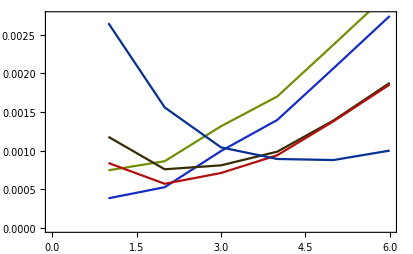

```mathematica
Show[ListLinePlot[aa[[1]],PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]],ListLinePlot[aa[[2]],PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]],ListLinePlot[aa[[3]],PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]],ListLinePlot[aa[[4]],PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]],ListLinePlot[aa[[5]],PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]],Frame->True]
```

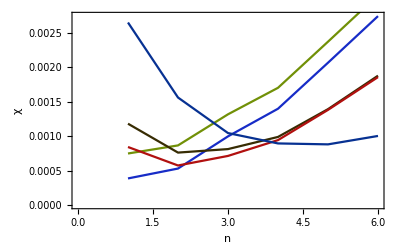

```mathematica
Show[%147,FrameLabel->{{HoldForm[χ],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]}]
```

```mathematica
9/14
```

9/14

```mathematica
N[9/14]
```

0.642857

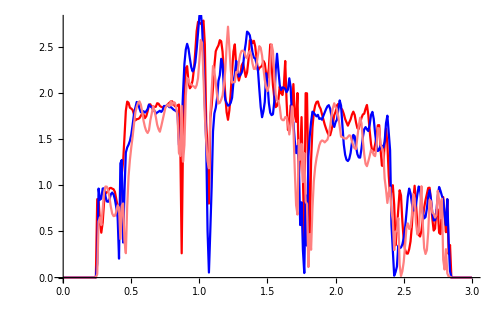

```mathematica
Show[ListLinePlot[%78[[2]],PlotStyle->Red],ListLinePlot[%78[[1]],PlotStyle->Blue],ListLinePlot[%78[[3]],PlotStyle->Pink]]
```

```mathematica
misfit[0.5]
```

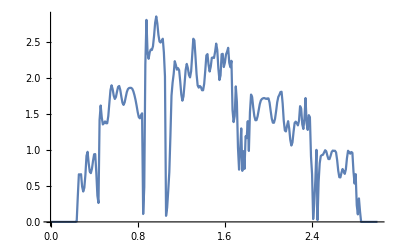

```mathematica
ListPlot[%23,Joined->True]
```

```mathematica
{imp[ω],imp[ω],imp[ω],imp1[ω],imp3[ω],imp5[ω],imp14[ω],imp[ω],imp[ω],imp[ω],imp2[ω],imp[ω],imp5[ω],imp[ω],imp4[ω],imp[ω],imp12[ω],imp1[ω],imp[ω],imp[ω],imp8[ω],imp[ω],imp[ω],imp8[ω],imp3[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp4[ω],imp[ω],imp11[ω],imp3[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp13[ω],imp7[ω],imp[ω],imp4[ω],imp7[ω],imp9[ω],imp[ω],imp2[ω],imp14[ω],imp5[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp13[ω],imp6[ω],imp[ω],imp[ω],imp10[ω],imp11[ω],imp[ω],imp12[ω],imp[ω],imp[ω],imp14[ω],imp[ω],imp[ω],imp[ω],imp11[ω],imp[ω],imp[ω],imp[ω],imp6[ω],imp[ω],imp1[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp6[ω],imp[ω],imp13[ω],imp9[ω],imp10[ω],imp2[ω],imp10[ω],imp7[ω],imp[ω],imp12[ω],imp[ω],imp8[ω],imp[ω],imp[ω],imp[ω],imp9[ω]}
```

{imp[ω],imp[ω],imp[ω],imp1[ω],imp3[ω],imp5[ω],imp14[ω],imp[ω],imp[ω],imp[ω],imp2[ω],imp[ω],imp5[ω],imp[ω],imp4[ω],imp[ω],imp12[ω],imp1[ω],imp[ω],imp[ω],imp8[ω],imp[ω],imp[ω],imp8[ω],imp3[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp4[ω],imp[ω],imp11[ω],imp3[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp13[ω],imp7[ω],imp[ω],imp4[ω],imp7[ω],imp9[ω],imp[ω],imp2[ω],imp14[ω],imp5[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp13[ω],imp6[ω],imp[ω],imp[ω],imp10[ω],imp11[ω],imp[ω],imp12[ω],imp[ω],imp[ω],imp14[ω],imp[ω],imp[ω],imp[ω],imp11[ω],imp[ω],imp[ω],imp[ω],imp6[ω],imp[ω],imp1[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp6[ω],imp[ω],imp13[ω],imp9[ω],imp10[ω],imp2[ω],imp10[ω],imp7[ω],imp[ω],imp12[ω],imp[ω],imp8[ω],imp[ω],imp[ω],imp[ω],imp9[ω]}

```mathematica
Part[%85[[;;20]]]
```

{imp[ω],imp[ω],imp[ω],imp1[ω],imp3[ω],imp5[ω],imp14[ω],imp[ω],imp[ω],imp[ω],imp2[ω],imp[ω],imp5[ω],imp[ω],imp4[ω],imp[ω],imp12[ω],imp1[ω],imp[ω],imp[ω]}

```mathematica
a5=Tally[Part[%85[[81;;100]]]]
```

{{imp[ω],10},{imp6[ω],1},{imp13[ω],1},{imp9[ω],2},{imp10[ω],2},{imp2[ω],1},{imp7[ω],1},{imp12[ω],1},{imp8[ω],1}}

```mathematica
a4=Tally[Part[%85[[61;;80]]]]
```

{{imp12[ω],1},{imp[ω],15},{imp14[ω],1},{imp11[ω],1},{imp6[ω],1},{imp1[ω],1}}

```mathematica
a3=Tally[Part[%85[[41;;60]]]]
```

{{imp7[ω],2},{imp[ω],9},{imp4[ω],1},{imp9[ω],1},{imp2[ω],1},{imp14[ω],1},{imp5[ω],1},{imp13[ω],1},{imp6[ω],1},{imp10[ω],1},{imp11[ω],1}}

```mathematica
a2=Tally[Part[%85[[21;;40]]]]
```

{{imp8[ω],2},{imp[ω],13},{imp3[ω],2},{imp4[ω],1},{imp11[ω],1},{imp13[ω],1}}

```mathematica
a1=Tally[Part[%85[[;;20]]]]
```

{{imp[ω],11},{imp1[ω],2},{imp3[ω],1},{imp5[ω],2},{imp14[ω],1},{imp2[ω],1},{imp4[ω],1},{imp12[ω],1}}

```mathematica
Join[RandomSample[Part[%85[[61;;80]]]],RandomSample[Part[%85[[21;;40]]]],RandomSample[Part[%85[[;;20]]]],RandomSample[Part[%85[[81;;100]]]],RandomSample[Part[%85[[41;;60]]]]]
```

{imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp12[ω],imp[ω],imp11[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp6[ω],imp[ω],imp[ω],imp14[ω],imp[ω],imp1[ω],imp8[ω],imp8[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp11[ω],imp[ω],imp3[ω],imp[ω],imp13[ω],imp[ω],imp3[ω],imp[ω],imp4[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp5[ω],imp14[ω],imp5[ω],imp1[ω],imp[ω],imp[ω],imp12[ω],imp2[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp4[ω],imp[ω],imp[ω],imp3[ω],imp[ω],imp1[ω],imp[ω],imp[ω],imp8[ω],imp10[ω],imp[ω],imp[ω],imp12[ω],imp[ω],imp6[ω],imp7[ω],imp10[ω],imp[ω],imp9[ω],imp[ω],imp13[ω],imp[ω],imp9[ω],imp[ω],imp[ω],imp2[ω],imp[ω],imp5[ω],imp[ω],imp13[ω],imp[ω],imp[ω],imp6[ω],imp7[ω],imp11[ω],imp7[ω],imp[ω],imp4[ω],imp2[ω],imp[ω],imp9[ω],imp[ω],imp[ω],imp10[ω],imp[ω],imp14[ω],imp[ω]}

```mathematica
Part[%85[[61;;80]]]
```

```mathematica
RandomSample[{imp12[ω],imp[ω],imp[ω],imp14[ω],imp[ω],imp[ω],imp[ω],imp11[ω],imp[ω],imp1[ω],imp[ω],imp6[ω],imp[ω],imp1[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω]}]
```

{imp[ω],imp[ω],imp1[ω],imp14[ω],imp12[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp11[ω],imp6[ω],imp[ω],imp1[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω]}

```mathematica
RandomSample[{imp2[ω],imp[ω],imp[ω],imp3[ω],imp[ω],imp[ω],imp[ω],imp11[ω],imp[ω],imp1[ω],imp[ω],imp4[ω],imp[ω],imp8[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω]}]
```

{imp8[ω],imp[ω],imp2[ω],imp[ω],imp[ω],imp[ω],imp11[ω],imp[ω],imp[ω],imp[ω],imp3[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp4[ω],imp[ω],imp[ω],imp[ω],imp1[ω]}

```mathematica
RandomSample[{imp[ω],imp[ω],imp[ω],imp1[ω],imp3[ω],imp5[ω],imp14[ω],imp[ω],imp[ω],imp[ω],imp2[ω],imp[ω],imp5[ω],imp[ω],imp4[ω],imp[ω],imp12[ω],imp1[ω],imp[ω],imp[ω]}]
```

{imp12[ω],imp[ω],imp1[ω],imp[ω],imp[ω],imp[ω],imp5[ω],imp5[ω],imp[ω],imp[ω],imp3[ω],imp2[ω],imp1[ω],imp[ω],imp[ω],imp14[ω],imp[ω],imp[ω],imp4[ω],imp[ω]}

```mathematica
RandomSample[{imp[ω],imp[ω],imp[ω],imp9[ω],imp1[ω],imp5[ω],imp14[ω],imp[ω],imp[ω],imp[ω],imp6[ω],imp[ω],imp7[ω],imp[ω],imp10[ω],imp[ω],imp8[ω],imp1[ω],imp[ω],imp[ω]}]
```

{imp[ω],imp[ω],imp[ω],imp1[ω],imp10[ω],imp[ω],imp[ω],imp1[ω],imp6[ω],imp8[ω],imp[ω],imp[ω],imp[ω],imp14[ω],imp9[ω],imp[ω],imp7[ω],imp[ω],imp[ω],imp5[ω]}

```mathematica
Part[%85[[41;;60]]]
```

```mathematica
RandomSample[{imp7[ω],imp1[ω],imp4[ω],imp7[ω],imp9[ω],imp[ω],imp2[ω],imp14[ω],imp5[ω],imp8[ω],imp[ω],imp5[ω],imp[ω],imp13[ω],imp6[ω],imp[ω],imp2[ω],imp10[ω],imp11[ω],imp[ω]}]
```

{imp2[ω],imp7[ω],imp[ω],imp[ω],imp8[ω],imp14[ω],imp[ω],imp5[ω],imp2[ω],imp5[ω],imp13[ω],imp[ω],imp6[ω],imp9[ω],imp11[ω],imp10[ω],imp4[ω],imp1[ω],imp[ω],imp7[ω]}

```mathematica
Join[RandomSample[%128],RandomSample[%130],RandomSample[%131],RandomSample[%132],RandomSample[%135]]
```

{imp[ω],imp[ω],imp12[ω],imp[ω],imp11[ω],imp1[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp6[ω],imp[ω],imp[ω],imp[ω],imp14[ω],imp1[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp[ω],imp3[ω],imp[ω],imp[ω],imp1[ω],imp2[ω],imp[ω],imp[ω],imp[ω],imp4[ω],imp[ω],imp[ω],imp11[ω],imp[ω],imp8[ω],imp[ω],imp[ω],imp[ω],imp12[ω],imp1[ω],imp[ω],imp[ω],imp1[ω],imp[ω],imp3[ω],imp[ω],imp14[ω],imp5[ω],imp[ω],imp2[ω],imp5[ω],imp[ω],imp4[ω],imp[ω],imp[ω],imp[ω],imp9[ω],imp[ω],imp[ω],imp[ω],imp14[ω],imp[ω],imp6[ω],imp1[ω],imp[ω],imp[ω],imp[ω],imp10[ω],imp7[ω],imp[ω],imp[ω],imp[ω],imp5[ω],imp1[ω],imp[ω],imp8[ω],imp10[ω],imp6[ω],imp5[ω],imp[ω],imp4[ω],imp1[ω],imp[ω],imp2[ω],imp[ω],imp7[ω],imp[ω],imp8[ω],imp13[ω],imp2[ω],imp14[ω],imp11[ω],imp9[ω],imp[ω],imp7[ω],imp5[ω]}

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14,imp15,imp16,imp17,imp18,imp19,imp20},12],Table[imp,8]]]
```

```mathematica
{imp,imp17,imp4,imp,imp,imp14,imp7,imp1,imp,imp,imp19,imp6,imp,imp,imp8,imp16,imp10,imp12,imp,imp13}
```

```mathematica
Table[{x,y},{x,Range[0,21,1]},{y,Range[0,21,1]}]
```

{{{0,0},{0,1},{0,2},{0,3},{0,4},{0,5},{0,6},{0,7},{0,8},{0,9},{0,10},{0,11},{0,12},{0,13},{0,14},{0,15},{0,16},{0,17},{0,18},{0,19},{0,20},{0,21}},{{1,0},{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{1,17},{1,18},{1,19},{1,20},{1,21}},{{2,0},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{2,11},{2,12},{2,13},{2,14},{2,15},{2,16},{2,17},{2,18},{2,19},{2,20},{2,21}},{{3,0},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{3,11},{3,12},{3,13},{3,14},{3,15},{3,16},{3,17},{3,18},{3,19},{3,20},{3,21}},{{4,0},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{4,11},{4,12},{4,13},{4,14},{4,15},{4,16},{4,17},{4,18},{4,19},{4,20},{4,21}},{{5,0},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,9},{5,10},{5,11},{5,12},{5,13},{5,14},{5,15},{5,16},{5,17},{5,18},{5,19},{5,20},{5,21}},{{6,0},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,9},{6,10},{6,11},{6,12},{6,13},{6,14},{6,15},{6,16},{6,17},{6,18},{6,19},{6,20},{6,21}},{{7,0},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13},{7,14},{7,15},{7,16},{7,17},{7,18},{7,19},{7,20},{7,21}},{{8,0},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,9},{8,10},{8,11},{8,12},{8,13},{8,14},{8,15},{8,16},{8,17},{8,18},{8,19},{8,20},{8,21}},{{9,0},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9},{9,10},{9,11},{9,12},{9,13},{9,14},{9,15},{9,16},{9,17},{9,18},{9,19},{9,20},{9,21}},{{10,0},{10,1},{10,2},{10,3},{10,4},{10,5},{10,6},{10,7},{10,8},{10,9},{10,10},{10,11},{10,12},{10,13},{10,14},{10,15},{10,16},{10,17},{10,18},{10,19},{10,20},{10,21}},{{11,0},{11,1},{11,2},{11,3},{11,4},{11,5},{11,6},{11,7},{11,8},{11,9},{11,10},{11,11},{11,12},{11,13},{11,14},{11,15},{11,16},{11,17},{11,18},{11,19},{11,20},{11,21}},{{12,0},{12,1},{12,2},{12,3},{12,4},{12,5},{12,6},{12,7},{12,8},{12,9},{12,10},{12,11},{12,12},{12,13},{12,14},{12,15},{12,16},{12,17},{12,18},{12,19},{12,20},{12,21}},{{13,0},{13,1},{13,2},{13,3},{13,4},{13,5},{13,6},{13,7},{13,8},{13,9},{13,10},{13,11},{13,12},{13,13},{13,14},{13,15},{13,16},{13,17},{13,18},{13,19},{13,20},{13,21}},{{14,0},{14,1},{14,2},{14,3},{14,4},{14,5},{14,6},{14,7},{14,8},{14,9},{14,10},{14,11},{14,12},{14,13},{14,14},{14,15},{14,16},{14,17},{14,18},{14,19},{14,20},{14,21}},{{15,0},{15,1},{15,2},{15,3},{15,4},{15,5},{15,6},{15,7},{15,8},{15,9},{15,10},{15,11},{15,12},{15,13},{15,14},{15,15},{15,16},{15,17},{15,18},{15,19},{15,20},{15,21}},{{16,0},{16,1},{16,2},{16,3},{16,4},{16,5},{16,6},{16,7},{16,8},{16,9},{16,10},{16,11},{16,12},{16,13},{16,14},{16,15},{16,16},{16,17},{16,18},{16,19},{16,20},{16,21}},{{17,0},{17,1},{17,2},{17,3},{17,4},{17,5},{17,6},{17,7},{17,8},{17,9},{17,10},{17,11},{17,12},{17,13},{17,14},{17,15},{17,16},{17,17},{17,18},{17,19},{17,20},{17,21}},{{18,0},{18,1},{18,2},{18,3},{18,4},{18,5},{18,6},{18,7},{18,8},{18,9},{18,10},{18,11},{18,12},{18,13},{18,14},{18,15},{18,16},{18,17},{18,18},{18,19},{18,20},{18,21}},{{19,0},{19,1},{19,2},{19,3},{19,4},{19,5},{19,6},{19,7},{19,8},{19,9},{19,10},{19,11},{19,12},{19,13},{19,14},{19,15},{19,16},{19,17},{19,18},{19,19},{19,20},{19,21}},{{20,0},{20,1},{20,2},{20,3},{20,4},{20,5},{20,6},{20,7},{20,8},{20,9},{20,10},{20,11},{20,12},{20,13},{20,14},{20,15},{20,16},{20,17},{20,18},{20,19},{20,20},{20,21}},{{21,0},{21,1},{21,2},{21,3},{21,4},{21,5},{21,6},{21,7},{21,8},{21,9},{21,10},{21,11},{21,12},{21,13},{21,14},{21,15},{21,16},{21,17},{21,18},{21,19},{21,20},{21,21}}}

```mathematica
Dimensions[%157]
```

{22,22,2}

```mathematica
p[z_]:=ListLinePlot[Table[{x,y},{x,Range[1,20,1]},{y,Range[1,20,1]}][[z]],PlotStyle->Gray]
```

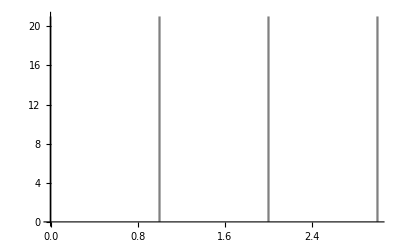

```mathematica
Show[p[1],p[2],p[3],p[4],PlotRange->All]
```

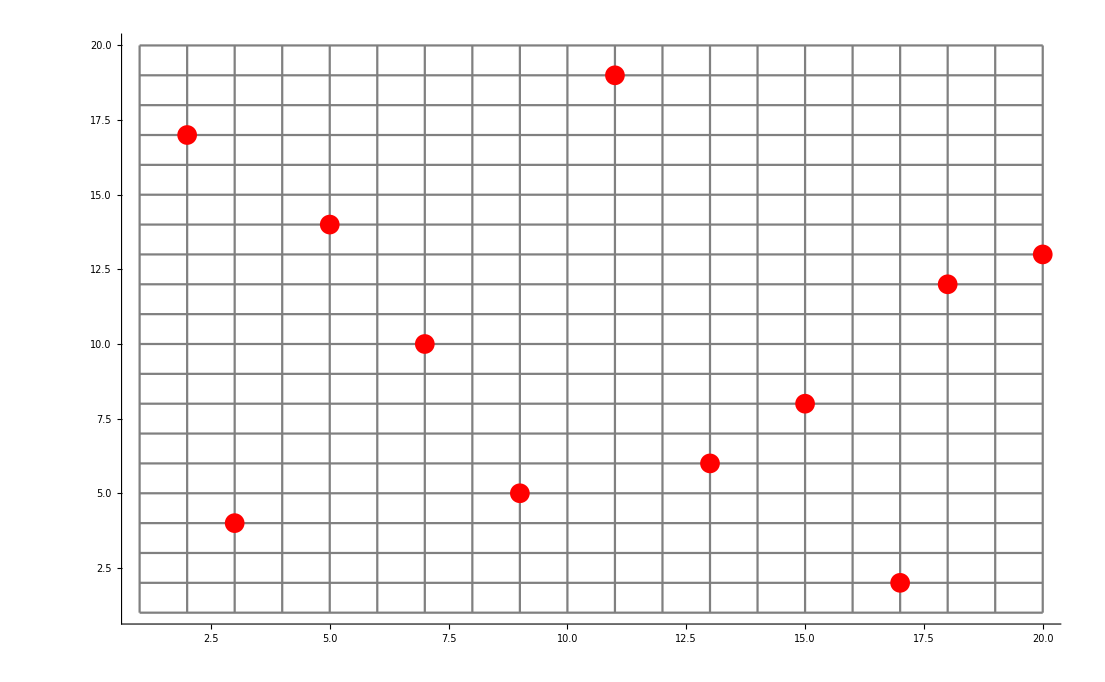

```mathematica
Show[Table[p[z],{z,20}],Table[q[z],{z,20}],ListPlot[{{2,17},{3,4},{5,14},{7,10},{11,19},{13,6},{15,8},{20,13},{18,12},{17,2},{9,5}},PlotStyle->Red],PlotRange->All]
```

```mathematica
line[z_]:=ListLinePlot[Table[{x,z},{x,Range[0,21,0.01]}],PlotStyle->Blue]
```

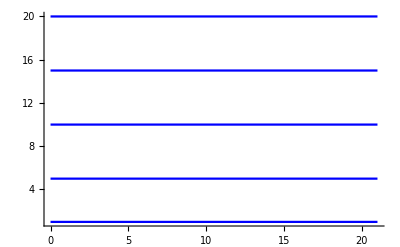

```mathematica
Show[line[1],line[5],line[10],line[15],line[20],PlotRange->All]
```

```mathematica
Show[%226,%228]
```

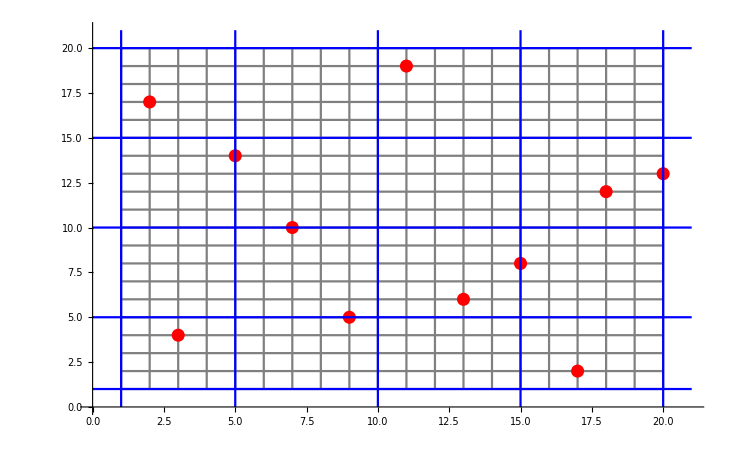

```mathematica
Show[%221,%229]
```

```mathematica
Show[%230,Axes->False]
```

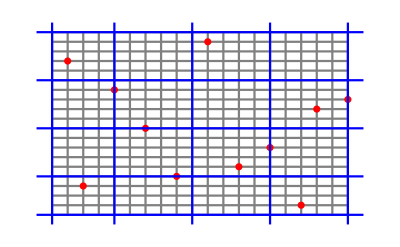

-Graphics-

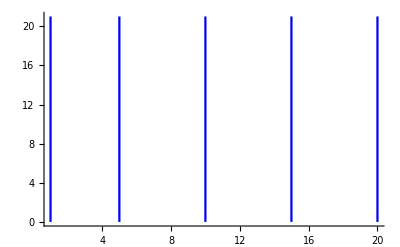

```mathematica
Show[line[1],line[5],line[10],line[15],line[20],PlotRange->All]
```

```mathematica
{imp,imp17,imp,imp3,imp9,imp13,imp,imp15,imp,imp7,imp,imp18,imp20,imp5,imp,imp,imp2,imp,imp11,imp}
```

```mathematica
q[z_]:=ListLinePlot[Transpose[Table[{x,y},{x,Range[1,20,1]},{y,Range[1,20,1]}]][[z]],PlotStyle->Gray]
```

```mathematica
Transpose[Join[{Transpose[{{2,17},{3,4},{6,14},{7,7},{8,1},{11,19},{12,6},{15,8},{20,13},{18,12},{17,10},{16,5}}][[2]]},{Transpose[{{2,17},{3,4},{6,14},{7,7},{8,1},{11,19},{12,6},{15,8},{20,13},{18,12},{17,10},{16,5}}][[1]]}]]
```

{{17,2},{4,3},{14,6},{7,7},{1,8},{19,11},{6,12},{8,15},{13,20},{12,18},{10,17},{5,16}}

```mathematica
SortBy[{{17,2},{4,3},{14,6},{7,7},{1,8},{19,11},{6,12},{8,15},{13,20},{12,18},{10,17},{5,16}},First]
```

{{1,8},{4,3},{5,16},{6,12},{7,7},{8,15},{10,17},{12,18},{13,20},{14,6},{17,2},{19,11}}

```mathematica
{imp8,imp,imp,imp3,imp16,imp12,imp7,imp15,imp,imp17,imp,imp18,imp20,imp6,imp,imp,imp2,imp,imp11,imp}
```

{imp8,imp,imp,imp3,imp16,imp12,imp7,imp15,imp,imp17,imp,imp18,imp20,imp6,imp,imp,imp2,imp,imp11,imp}

```mathematica
Length[{imp8,imp,imp,imp3,imp16,imp12,imp7,imp15,imp,imp17,imp,imp18,imp20,imp6,imp,imp,imp,imp2,imp,imp11,imp}]
```

21

```mathematica
pp[z_]:=ListLinePlot[Table[{x,y},{x,Range[0,20,5]},{y,Range[1,20,5]}][[z]],PlotStyle->Blue]
```

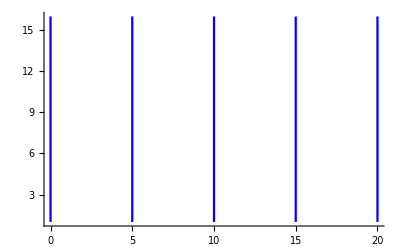

```mathematica
Show[pp[2],pp[1],pp[3],pp[4],pp[5],PlotRange->All]
```

```mathematica
Table[{x,y},{x,Range[1,20,4]},{y,Range[1,20,4]}]
```

{{{1,1},{1,5},{1,9},{1,13},{1,17}},{{5,1},{5,5},{5,9},{5,13},{5,17}},{{9,1},{9,5},{9,9},{9,13},{9,17}},{{13,1},{13,5},{13,9},{13,13},{13,17}},{{17,1},{17,5},{17,9},{17,13},{17,17}}}

```mathematica
{{2,17},{3,4},{5,14},{7,10},{11,19},{13,6},{15,8},{20,13},{18,12},{17,2},{9,5}}
```

{{2,17},{3,4},{5,14},{7,10},{11,19},{13,6},{15,8},{20,13},{18,12},{17,2},{9,5}}

```mathematica
SortBy[{{2,17},{3,4},{5,14},{7,10},{11,19},{13,6},{15,8},{20,13},{18,12},{17,2},{9,5}},First]
```

```mathematica
{{2,imp17},{3,imp4},{5,imp14},{7,imp10},{9,imp5},{11,imp19},{13,imp6},{15,imp8},{17,imp2},{18,imp12},{20,imp13}}
```

```mathematica
{{1,imp},{2,imp17},{3,imp4},{4,imp},{5,imp14},{6,imp},{7,imp10},{8,imp},{9,imp5},{10,imp},{11,imp19},{12,imp},{13,imp6},{14,imp},{15,imp8},{16,imp},{17,imp2},{18,imp12},{19,imp},{20,imp13}}
```

{{1,imp},{2,imp17},{3,imp4},{4,imp},{5,imp14},{6,imp},{7,imp10},{8,imp},{9,imp5},{10,imp},{11,imp19},{12,imp},{13,imp6},{14,imp},{15,imp8},{16,imp},{17,imp2},{18,imp12},{19,imp},{20,imp13}}

```mathematica
Transpose[%219]
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{imp,imp17,imp4,imp,imp14,imp,imp10,imp,imp5,imp,imp19,imp,imp6,imp,imp8,imp,imp2,imp12,imp,imp13}}